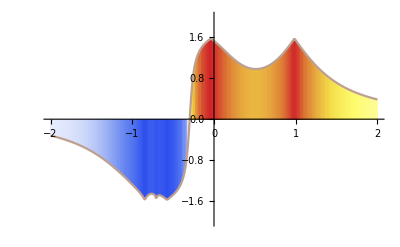

```mathematica
Clear["`*"]
L1=Transpose@RandomReal[{-1,1},{5,2}];
fun=Inner@@Join[{Function[{a,b},a/Abs[#-b]]},L1,{Plus}]&;
data=Table[{i,ArcTan@fun[i]},{i,-2,2,0.01}];
ListLinePlot[data,Filling->Axis,ColorFunction->"TemperatureMap",PlotRange->{-2,2}]
```

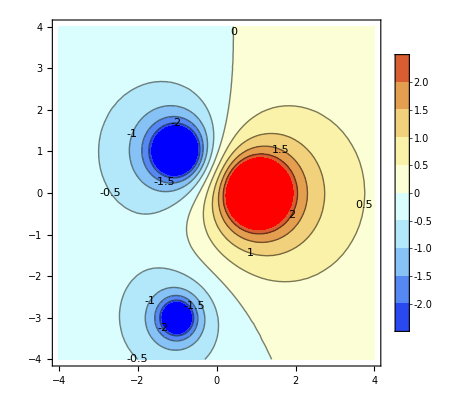

-Graphics3D-

```mathematica
Clear["`*"]
ElectroStaticPotential[{q_,p_},r_]:=Sum[q[[i]]/Norm[r-p[[i]]],{i,Length[q]}];
func=ElectroStaticPotential[{{-1,-2,3},{{-1,-3},{-1,1},{1,0}}}, {x,y}];
ContourPlot[func,{x,-4,4},{y,-4,4},ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,ContourLabels->All, ClippingStyle->{Blue,Red}]
Plot3D[func,{x,-4,4},{y,-4,4},ColorFunction->"LightTemperatureMap",PlotLegends->Automatic, ClippingStyle->{Blue,Red}]
```

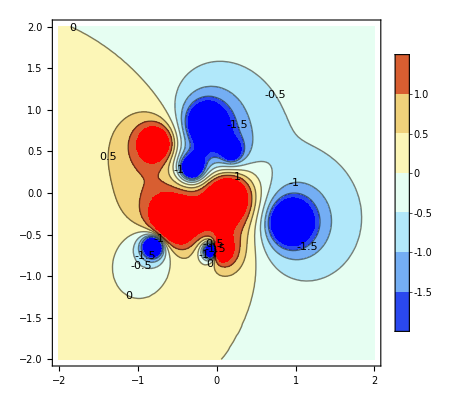

-Graphics3D-

```mathematica
Clear["`*"]
ElectroStaticPotential[q_,p_,r_]:=Sum[q[[i]]/Norm[r-p[[i]]],{i,Length[q]}];
func=ElectroStaticPotential[RandomReal[{-1,1},10],RandomReal[{-1,1},{10,2}], {x,y}];
ContourPlot[func,{x,-2,2},{y,-2,2},ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,ContourLabels->All, ClippingStyle->{Blue,Red}]
Plot3D[func,{x,-2,2},{y,-2,2},ColorFunction->"LightTemperatureMap",PlotLegends->Automatic, ClippingStyle->{Blue,Red}]
```

```mathematica
Table[ContourPlot[Evaluate[Sum[Product[Norm[{x,y}-RandomReal[{-3,3},{2}]],{i,j}]/Product[Norm[{x,y}-RandomReal[{-3,3},{2}]],{i,j}],{j,1,5}]], {x, -5, 5}, {y, -5, 5}, Contours->50,ColorFunction->(Hue[#]&), ClippingStyle->Automatic,FrameTicks->None],{3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ContourPlot[Re[f[x+I y]],{x,-Pi,Pi},{y,-Pi,Pi},PlotLabel->f,FrameTicks->{{-Pi,0,Pi},{-Pi,0,Pi}},ClippingStyle->Automatic,ColorFunction->"Pastel"],{f,{ArcSin,ArcCos,ArcCsc,ArcSec,ArcTan,ArcCot}}]
```